```mathematica
ClearAll["Global`*"]
Rx = (1/(√2))*({{√2, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, -1}, {0, 0, 1, 0, 1, 0}, {0, 0, 0, √2, 0, 0}, {0, 1, 0, 0, 0, 1}, {0, 0, 1, 0, -1, 0}});
```

```mathematica
Bx = ({{0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -1}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, -1, 0, 0, 0, 0}});
```

```mathematica
(*Sm3 =1/Δ *DiagonalMatrix[{0,0,0,-1/12,-1/12,-1/12}];
Sm2 =1/Δ * DiagonalMatrix[{0,0,0,1/2,1/2,1/2}];
Sm1 =1/Δ * DiagonalMatrix[{-1/4,-1/4,-1/4,-3/2,-3/2,-3/2}];
S0=1/Δ * DiagonalMatrix[{(- 5)/6,(- 5)/6,-5/6,5/6,5/6,5/6}];
Sp1 = 1/Δ *DiagonalMatrix[{3/2,3/2,3/2,1/4,1/4,1/4}];
Sp2 =1/Δ * DiagonalMatrix[{-1/2,-1/2,-1/2,0,0,0}];
Sp3 =1/Δ * DiagonalMatrix[{1/12,1/12,1/12,0,0,0}];
*)
```

```mathematica
Sp = 1/Δ *{0, 0, -1/4, -5/6, 3/2, -1/2, 1/12};
Sm = 1/Δ *{-1/12, 1/2, -3/2, 5/6, 1/4, 0, 0};
Sps1 = 1/Δ *{0,0,-16/60,-45/60,80/60,-20/60,1/60};
Sps2 = 1/Δ *{0,0,-75/240,-128/240,225/240,-25/240,3/240};
Sps3 = 1/Δ *{0,0,-192/210,+35/210,1,-63/210,10/210}/2;
Sms1 =1/Δ *{-8/30,45/30,-120/30,80/30,3/30,0,0}/2;
Sms2 = 1/Δ *{-15/30,64/30,-90/30,35/30,6/30,0,0}/2;
Sms3 = 1/Δ *{-64/210,175/210,-350/210,189/210,50/210,0,0}/2;
SpTest = (1/Δ)*{0,0, 0, 0, -25/12, 48/12, -36/12, 16/12,-3/12};
SmTest = (1/Δ)*{3/12,-16/12, 36/12, -48/12, 25/12,0,0,0,0};
(*SpO8 =1/Δ{0, 0, 0, 0,15/840,-240/840,-798/840,1680/840,-1050/840,560/840,-210/840,48/840,-5/840} -2,-1,0,1,2,3,4,5,6  X imaginary part negative!*) 
(*SmO8 =1/Δ{5/840,-48/840,210/840,-560/840,1050/840,-1680/840,798/840,240/840,-15/840,0,0,0,0}-6,-5,-4,-3,-2,-1,0,1,2 X imaginary part negative!*)
(*SpO8 =1/Δ{0,0, 0, 0, 0,0,-105/840,-1338/840,2940/840,-2940/840,2450/840,-1470/840,588/840,-140/840,15/840} -1,0,1,2,3,4,5,6,7 X imaginary part negative!*) 
(*SmO8 =1/Δ{-15/840,140/840,-588/840,1470/840,-2450/840,2940/840,-2940/840,1338/840,105/840,0,0,0,0,0,0} -7,-6,-5,-4,-3,-2,-1,0,1 X imaginary part negative!*)

(* SpO9 =1/Δ{0, 0, 0, -10/2520,135/2520,-1080/2520,-1554/2520,3780/2520,-1890/2520,840/2520,-270/2520,54/2520,-5/2520} -3,-2,-1,0,1,2,3,4,5,6 X imaginary part negative!*)
(* SmO9 =1/Δ{5/2520,-54/2520,270/2520,-840/2520,1890/2520,-3780/2520,1554/2520,1080/2520,-135/2520,10/2520,0,0,0} -6,-5,-4,-3,-2,-1,0,1,2,3 X imaginary part negative!*)
(* SpO7 =1/Δ 1/420{ 0, 0,0,10,-140,-329,700,-350,140,-35,4} -3,-2,-1,0,1,2,3,4,5,6 X imaginary part negative!*)
(* SmO7 =1/Δ 1/420{-4,35,-140,350,-700,329,140,-10,0,0,0} -5,-4,-3,-2,-1,0,1,2 X imaginary part negative!*)
SpO7={0,0,0,0,0,0,0,0,0,0,0};
SmO7={0,0,0,0,0,0,0,0,0,0,0};
SpO9 =1/2520 1/Δ{ 0, 0, 3, -40,270,-1440,-924,3024,-1260,480,-135,24,-2};(*4,-3,-2,-1,0,1,2,3,4,5,6*)
SmO9 =1/2520 1/Δ{2,-24,135,-480,1260,-3024,924,1440,-270,40,-3,0,0};(*-6,-5,-4,-3,-2,-1,0,1,2,3,4*)


Spb := Sp;
Smb :=Sm;
Sm3=DiagonalMatrix[{Spb[[1]],Spb[[1]],Spb[[1]],Smb[[1]],Smb[[1]],Smb[[1]]}];
Sm2 =DiagonalMatrix[{Spb[[2]],Spb[[2]],Spb[[2]],Smb[[2]],Smb[[2]],Smb[[2]]}];
Sm1=DiagonalMatrix[{Spb[[3]],Spb[[3]],Spb[[3]],Smb[[3]],Smb[[3]],Smb[[3]]}];
S0= DiagonalMatrix[{Spb[[4]],Spb[[4]],Spb[[4]],Smb[[4]],Smb[[4]],Smb[[4]]}];
Sp1 = DiagonalMatrix[{Spb[[5]],Spb[[5]],Spb[[5]],Smb[[5]],Smb[[5]],Smb[[5]]}];
Sp2 = DiagonalMatrix[{Spb[[6]],Spb[[6]],Spb[[6]],Smb[[6]],Smb[[6]],Smb[[6]]}];
Sp3 = DiagonalMatrix[{Spb[[7]],Spb[[7]],Spb[[7]],Smb[[7]],Smb[[7]],Smb[[7]]}];

(*Sps1, Sm*)
Spb := Sps1;
Smb := Sm;

Sm3b=DiagonalMatrix[{Spb[[1]],Spb[[1]],Spb[[1]],Smb[[1]],Smb[[1]],Smb[[1]]}];
Sm2b =DiagonalMatrix[{Spb[[2]],Spb[[2]],Spb[[2]],Smb[[2]],Smb[[2]],Smb[[2]]}];
Sm1b=DiagonalMatrix[{Spb[[3]],Spb[[3]],Spb[[3]],Smb[[3]],Smb[[3]],Smb[[3]]}];
S0b= DiagonalMatrix[{Spb[[4]],Spb[[4]],Spb[[4]],Smb[[4]],Smb[[4]],Smb[[4]]}];
Sp1b = DiagonalMatrix[{Spb[[5]],Spb[[5]],Spb[[5]],Smb[[5]],Smb[[5]],Smb[[5]]}];
Sp2b = DiagonalMatrix[{Spb[[6]],Spb[[6]],Spb[[6]],Smb[[6]],Smb[[6]],Smb[[6]]}];
Sp3b = DiagonalMatrix[{Spb[[7]],Spb[[7]],Spb[[7]],Smb[[7]],Smb[[7]],Smb[[7]]}];

xm3b[kx_]=Bx.Transpose[Rx].Sm3b.Rx*Exp[-I*(-3)*kx*Δ];
xm2b[kx_ ]=Bx.Transpose[Rx].Sm2b.Rx*Exp[-I*(-2)*kx*Δ];
xm1b[kx_]=Bx.Transpose[Rx].Sm1b.Rx*Exp[-I*(-1)*kx*Δ];
x0b[kx_ ]=Bx.Transpose[Rx].S0b.Rx;

xp3b[kx_]=Bx.Transpose[Rx].Sp3b.Rx*Exp[-I*4*kx*Δ];
xp2b[kx_]=Bx.Transpose[Rx].Sp2b.Rx*Exp[-I*2*kx*Δ];
xp1b[kx_]=Bx.Transpose[Rx].Sp1b.Rx*Exp[-I*1*kx*Δ];
sumb1[kx_]=xm3b [kx]+xm2b[kx]+xm1b [kx]+x0b [kx]+xp1b [kx]+xp2b[kx]+xp3b [kx];

(*Sps2, Sm*)
Spb := Sps2;
Smb := Sm;

Sm3b=DiagonalMatrix[{Spb[[1]],Spb[[1]],Spb[[1]],Smb[[1]],Smb[[1]],Smb[[1]]}];
Sm2b =DiagonalMatrix[{Spb[[2]],Spb[[2]],Spb[[2]],Smb[[2]],Smb[[2]],Smb[[2]]}];
Sm1b=DiagonalMatrix[{Spb[[3]],Spb[[3]],Spb[[3]],Smb[[3]],Smb[[3]],Smb[[3]]}];
S0b= DiagonalMatrix[{Spb[[4]],Spb[[4]],Spb[[4]],Smb[[4]],Smb[[4]],Smb[[4]]}];
Sp1b = DiagonalMatrix[{Spb[[5]],Spb[[5]],Spb[[5]],Smb[[5]],Smb[[5]],Smb[[5]]}];
Sp2b = DiagonalMatrix[{Spb[[6]],Spb[[6]],Spb[[6]],Smb[[6]],Smb[[6]],Smb[[6]]}];
Sp3b = DiagonalMatrix[{Spb[[7]],Spb[[7]],Spb[[7]],Smb[[7]],Smb[[7]],Smb[[7]]}];

xm3b[kx_]=Bx.Transpose[Rx].Sm3b.Rx*Exp[-I*(-3)*kx*Δ];
xm2b[kx_ ]=Bx.Transpose[Rx].Sm2b.Rx*Exp[-I*(-2)*kx*Δ];
xm1b[kx_]=Bx.Transpose[Rx].Sm1b.Rx*Exp[-I*(-1)*kx*Δ];
x0b[kx_ ]=Bx.Transpose[Rx].S0b.Rx;

xp3b[kx_]=Bx.Transpose[Rx].Sp3b.Rx*Exp[-I*5*kx*Δ];
xp2b[kx_]=Bx.Transpose[Rx].Sp2b.Rx*Exp[-I*3*kx*Δ];
xp1b[kx_]=Bx.Transpose[Rx].Sp1b.Rx*Exp[-I*1*kx*Δ];
sumb2[kx_]=xm3b [kx]+xm2b[kx]+xm1b [kx]+x0b [kx]+xp1b [kx]+xp2b[kx]+xp3b [kx];

(*Sps3, Sms1*)
Spb := Sps3;
Smb := Sms1;

Sm3b=DiagonalMatrix[{Spb[[1]],Spb[[1]],Spb[[1]],Smb[[1]],Smb[[1]],Smb[[1]]}];
Sm2b =DiagonalMatrix[{Spb[[2]],Spb[[2]],Spb[[2]],Smb[[2]],Smb[[2]],Smb[[2]]}];
Sm1b=DiagonalMatrix[{Spb[[3]],Spb[[3]],Spb[[3]],Smb[[3]],Smb[[3]],Smb[[3]]}];
S0b= DiagonalMatrix[{Spb[[4]],Spb[[4]],Spb[[4]],Smb[[4]],Smb[[4]],Smb[[4]]}];
Sp1b = DiagonalMatrix[{Spb[[5]],Spb[[5]],Spb[[5]],Smb[[5]],Smb[[5]],Smb[[5]]}];
Sp2b = DiagonalMatrix[{Spb[[6]],Spb[[6]],Spb[[6]],Smb[[6]],Smb[[6]],Smb[[6]]}];
Sp3b = DiagonalMatrix[{Spb[[7]],Spb[[7]],Spb[[7]],Smb[[7]],Smb[[7]],Smb[[7]]}];

xm3b[kx_]=Bx.Transpose[Rx].Sm3b.Rx*Exp[-I*(-3)*kx*Δ];
xm2b[kx_ ]=Bx.Transpose[Rx].Sm2b.Rx*Exp[-I*(-2)*kx*Δ];
xm1b[kx_]=Bx.Transpose[Rx].Sm1b.Rx*Exp[-I*(-1)*kx*Δ];
x0b[kx_ ]=Bx.Transpose[Rx].S0b.Rx;

xp3b[kx_]=Bx.Transpose[Rx].Sp3b.Rx*Exp[-I*6*kx*Δ];
xp2b[kx_]=Bx.Transpose[Rx].Sp2b.Rx*Exp[-I*4*kx*Δ];
xp1b[kx_]=Bx.Transpose[Rx].Sp1b.Rx*Exp[-I*2*kx*Δ];
sumb3[kx_]=xm3b [kx]+xm2b[kx]+xm1b [kx]+x0b [kx]+xp1b [kx]+xp2b[kx]+xp3b [kx];

(*Sp, Sms2*)
Spb := Sp/2;
Smb := Sms2;

Sm3b=DiagonalMatrix[{Spb[[1]],Spb[[1]],Spb[[1]],Smb[[1]],Smb[[1]],Smb[[1]]}];
Sm2b =DiagonalMatrix[{Spb[[2]],Spb[[2]],Spb[[2]],Smb[[2]],Smb[[2]],Smb[[2]]}];
Sm1b=DiagonalMatrix[{Spb[[3]],Spb[[3]],Spb[[3]],Smb[[3]],Smb[[3]],Smb[[3]]}];
S0b= DiagonalMatrix[{Spb[[4]],Spb[[4]],Spb[[4]],Smb[[4]],Smb[[4]],Smb[[4]]}];
Sp1b = DiagonalMatrix[{Spb[[5]],Spb[[5]],Spb[[5]],Smb[[5]],Smb[[5]],Smb[[5]]}];
Sp2b = DiagonalMatrix[{Spb[[6]],Spb[[6]],Spb[[6]],Smb[[6]],Smb[[6]],Smb[[6]]}];
Sp3b = DiagonalMatrix[{Spb[[7]],Spb[[7]],Spb[[7]],Smb[[7]],Smb[[7]],Smb[[7]]}];

xm3b[kx_]=Bx.Transpose[Rx].Sm3b.Rx*Exp[-I*(-4)*kx*Δ];
xm2b[kx_ ]=Bx.Transpose[Rx].Sm2b.Rx*Exp[-I*(-3)*kx*Δ];
xm1b[kx_]=Bx.Transpose[Rx].Sm1b.Rx*Exp[-I*(-2)*kx*Δ];
x0b[kx_ ]=Bx.Transpose[Rx].S0b.Rx;

xp3b[kx_]=Bx.Transpose[Rx].Sp3b.Rx*Exp[-I*6*kx*Δ];
xp2b[kx_]=Bx.Transpose[Rx].Sp2b.Rx*Exp[-I*4*kx*Δ];
xp1b[kx_]=Bx.Transpose[Rx].Sp1b.Rx*Exp[-I*2*kx*Δ];
sumb4[kx_]=xm3b [kx]+xm2b[kx]+xm1b [kx]+x0b [kx]+xp1b [kx]+xp2b[kx]+xp3b [kx];

(*Sp, Sms3*)
Spb := Sp/2;
Smb := Sms3;

Sm3b=DiagonalMatrix[{Spb[[1]],Spb[[1]],Spb[[1]],Smb[[1]],Smb[[1]],Smb[[1]]}];
Sm2b =DiagonalMatrix[{Spb[[2]],Spb[[2]],Spb[[2]],Smb[[2]],Smb[[2]],Smb[[2]]}];
Sm1b=DiagonalMatrix[{Spb[[3]],Spb[[3]],Spb[[3]],Smb[[3]],Smb[[3]],Smb[[3]]}];
S0b= DiagonalMatrix[{Spb[[4]],Spb[[4]],Spb[[4]],Smb[[4]],Smb[[4]],Smb[[4]]}];
Sp1b = DiagonalMatrix[{Spb[[5]],Spb[[5]],Spb[[5]],Smb[[5]],Smb[[5]],Smb[[5]]}];
Sp2b = DiagonalMatrix[{Spb[[6]],Spb[[6]],Spb[[6]],Smb[[6]],Smb[[6]],Smb[[6]]}];
Sp3b = DiagonalMatrix[{Spb[[7]],Spb[[7]],Spb[[7]],Smb[[7]],Smb[[7]],Smb[[7]]}];

xm3b[kx_]=Bx.Transpose[Rx].Sm3b.Rx*Exp[-I*(-5)*kx*Δ];
xm2b[kx_ ]=Bx.Transpose[Rx].Sm2b.Rx*Exp[-I*(-4)*kx*Δ];
xm1b[kx_]=Bx.Transpose[Rx].Sm1b.Rx*Exp[-I*(-2)*kx*Δ];
x0b[kx_ ]=Bx.Transpose[Rx].S0b.Rx;

xp3b[kx_]=Bx.Transpose[Rx].Sp3b.Rx*Exp[-I*6*kx*Δ];
xp2b[kx_]=Bx.Transpose[Rx].Sp2b.Rx*Exp[-I*4*kx*Δ];
xp1b[kx_]=Bx.Transpose[Rx].Sp1b.Rx*Exp[-I*2*kx*Δ];
sumb5[kx_]=xm3b [kx]+xm2b[kx]+xm1b [kx]+x0b [kx]+xp1b [kx]+xp2b[kx]+xp3b [kx];
```

```mathematica
(*Normal Regular Grid*)
xm3[kx_]=Bx.Transpose[Rx].Sm3.Rx*Exp[-I*(-3)*kx*Δ];
xm2[kx_ ]=Bx.Transpose[Rx].Sm2.Rx*Exp[-I*(-2)*kx*Δ];
xm1[kx_]=Bx.Transpose[Rx].Sm1.Rx*Exp[-I*(-1)*kx*Δ];
x0[kx_ ]=Bx.Transpose[Rx].S0.Rx;

xp3[kx_]=Bx.Transpose[Rx].Sp3.Rx*Exp[-I*3*kx*Δ];
xp2[kx_]=Bx.Transpose[Rx].Sp2.Rx*Exp[-I*2*kx*Δ];
xp1[kx_]=Bx.Transpose[Rx].Sp1.Rx*Exp[-I*1*kx*Δ];
sum[kx_]=xm3 [kx]+xm2[kx]+xm1 [kx]+x0 [kx]+xp1 [kx]+xp2 [kx]+xp3 [kx];

(*Alternative Stencil Regular Grid*)
Spb := SpTest;
Smb :=SmTest;

Sm4t=DiagonalMatrix[{Spb[[1]],Spb[[1]],Spb[[1]],Smb[[1]],Smb[[1]],Smb[[1]]}];
Sm3t =DiagonalMatrix[{Spb[[2]],Spb[[2]],Spb[[2]],Smb[[2]],Smb[[2]],Smb[[2]]}];
Sm2t=DiagonalMatrix[{Spb[[3]],Spb[[3]],Spb[[3]],Smb[[3]],Smb[[3]],Smb[[3]]}];
Sm1t= DiagonalMatrix[{Spb[[4]],Spb[[4]],Spb[[4]],Smb[[4]],Smb[[4]],Smb[[4]]}];
S0t = DiagonalMatrix[{Spb[[5]],Spb[[5]],Spb[[5]],Smb[[5]],Smb[[5]],Smb[[5]]}];
Sp1t = DiagonalMatrix[{Spb[[6]],Spb[[6]],Spb[[6]],Smb[[6]],Smb[[6]],Smb[[6]]}];
Sp2t = DiagonalMatrix[{Spb[[7]],Spb[[7]],Spb[[7]],Smb[[7]],Smb[[7]],Smb[[7]]}];
Sp3t = DiagonalMatrix[{Spb[[8]],Spb[[8]],Spb[[8]],Smb[[8]],Smb[[8]],Smb[[8]]}];
Sp4t = DiagonalMatrix[{Spb[[9]],Spb[[9]],Spb[[9]],Smb[[9]],Smb[[9]],Smb[[9]]}];

xm4t[kx_]=Bx.Transpose[Rx].Sm4t.Rx*Exp[-I*(-4)*kx*Δ];
xm3t[kx_]=Bx.Transpose[Rx].Sm3t.Rx*Exp[-I*(-3)*kx*Δ];
xm2t[kx_ ]=Bx.Transpose[Rx].Sm2t.Rx*Exp[-I*(-2)*kx*Δ];
xm1t[kx_]=Bx.Transpose[Rx].Sm1t.Rx*Exp[-I*(-1)*kx*Δ];
x0t[kx_ ]=Bx.Transpose[Rx].S0t.Rx;

xp4t[kx_]=Bx.Transpose[Rx].Sp3t.Rx*Exp[-I*4*kx*Δ];
xp3t[kx_]=Bx.Transpose[Rx].Sp3t.Rx*Exp[-I*3*kx*Δ];
xp2t[kx_]=Bx.Transpose[Rx].Sp2t.Rx*Exp[-I*2*kx*Δ];
xp1t[kx_]=Bx.Transpose[Rx].Sp1t.Rx*Exp[-I*1*kx*Δ];
sumTest[kx_]=xm4t [kx]+xm3t [kx]+xm2t[kx]+xm1t [kx]+x0t [kx]+xp1t [kx]+xp2t [kx]+xp3t [kx]+xp4t [kx];

(*Interpolated grid points 1*)
xm3i1[kx_]=Bx.Transpose[Rx].Sm3.Rx*Exp[-I*(-3)*kx*Δ];
xm2i1[kx_ ]=Bx.Transpose[Rx].Sm2.Rx*Exp[-I*(-2)*kx*Δ];
xm1i1[kx_]=Bx.Transpose[Rx].Sm1.Rx*Exp[-I*(-1)*kx*Δ];
x0i1[kx_ ]=Bx.Transpose[Rx].S0.Rx;

xp3i1[kx_]=Bx.Transpose[Rx].Sp3.Rx*(Exp[-I*2*kx*Δ] + Exp[-I*4*kx*Δ] )/2;
xp2i1[kx_]=Bx.Transpose[Rx].Sp2.Rx*Exp[-I*2*kx*Δ];
xp1i1[kx_]=Bx.Transpose[Rx].Sp1.Rx*Exp[-I*1*kx*Δ];
sumi1[kx_]=xm3i1[kx]+xm2i1[kx]+xm1i1 [kx]+x0i1[kx]+xp1i1[kx]+xp2i1 [kx]+xp3i1[kx];

(*Interpolated grid points 2*)
xm3i2[kx_]=Bx.Transpose[Rx].Sm3.Rx*Exp[-I*(-3)*kx*Δ];
xm2i2[kx_ ]=Bx.Transpose[Rx].Sm2.Rx*Exp[-I*(-2)*kx*Δ];
xm1i2[kx_]=Bx.Transpose[Rx].Sm1.Rx*Exp[-I*(-1)*kx*Δ];
x0i2[kx_ ]=Bx.Transpose[Rx].S0.Rx;

xp3i2[kx_]=Bx.Transpose[Rx].Sp3.Rx*(Exp[-I*2*kx*Δ] + Exp[-I*4*kx*Δ] )/2;
xp2i2[kx_]=Bx.Transpose[Rx].Sp2.Rx*Exp[-I*2*kx*Δ];
xp1i2[kx_]=Bx.Transpose[Rx].Sp1.Rx*(1 + Exp[-I*2*kx*Δ])/2;
sumi2[kx_]=xm3i2[kx]+xm2i2[kx]+xm1i2[kx]+x0i2[kx]+xp1i2[kx]+xp2i2[kx]+xp3i2[kx];

(*Interpolated grid points 3*)
xm3i3[kx_]=Bx.Transpose[Rx].Sm3.Rx*Exp[-I*(-3)*kx*Δ];
xm2i3[kx_ ]=Bx.Transpose[Rx].Sm2.Rx*(Exp[-I*(-1)*kx*Δ]+Exp[-I*(-3)*kx*Δ])/2;
xm1i3[kx_]=Bx.Transpose[Rx].Sm1.Rx*Exp[-I*(-1)*kx*Δ];
x0i3[kx_ ]=Bx.Transpose[Rx].S0.Rx(Exp[-I*(-1)*kx*Δ]+Exp[-I*1*kx*Δ])/2;

xp3i3[kx_]=Bx.Transpose[Rx].Sp3.Rx*Exp[-I*3*kx*Δ];
xp2i3[kx_]=Bx.Transpose[Rx].Sp2.Rx*(Exp[-I*1*kx*Δ] + Exp[-I*3*kx*Δ])/2;
xp1i3[kx_]=Bx.Transpose[Rx].Sp1.Rx*Exp[-I*1*kx*Δ];
sumi3[kx_]=xm3i3[kx]+xm2i3[kx]+xm1i3[kx]+x0i3[kx]+xp1i3[kx]+xp2i3[kx]+xp3i3[kx];
```

```mathematica
(*Grid with Half Resolution*)
xm32[kx_]=Bx.Transpose[Rx].Sm3.Rx*Exp[-I*(-6)*kx*Δ]/2;
xm22[kx_ ]=Bx.Transpose[Rx].Sm2.Rx*Exp[-I*(-4)*kx*Δ]/2;
xm12[kx_]=Bx.Transpose[Rx].Sm1.Rx*Exp[-I*(-2)*kx*Δ]/2;
x02[kx_ ]=Bx.Transpose[Rx].S0.Rx /2;

xp32[kx_]=Bx.Transpose[Rx].Sp3.Rx*Exp[-I*6*kx*Δ]/2;
xp22[kx_]=Bx.Transpose[Rx].Sp2.Rx*Exp[-I*4*kx*Δ]/2;
xp12[kx_]=Bx.Transpose[Rx].Sp1.Rx*Exp[-I*2*kx*Δ]/2;
sum2[kx_]=xm32 [kx]+xm22[kx]+xm12 [kx]+x02[kx]+xp12[kx]+xp22[kx]+xp32[kx];

(*Grid Order 7*)
Spb := SpO7;
Smb :=SmO7;
ix = 1;
Sm5o2=DiagonalMatrix[{Spb[[ix]],Spb[[ix]],Spb[[ix]],Smb[[ix]],Smb[[ix]],Smb[[ix]]}];
ix +=1;
Sm4o2=DiagonalMatrix[{Spb[[ix]],Spb[[ix]],Spb[[ix]],Smb[[ix]],Smb[[ix]],Smb[[ix]]}];
ix +=1;
Sm3o2=DiagonalMatrix[{Spb[[ix]],Spb[[ix]],Spb[[ix]],Smb[[ix]],Smb[[ix]],Smb[[ix]]}];
ix +=1;
Sm2o2=DiagonalMatrix[{Spb[[ix]],Spb[[ix]],Spb[[ix]],Smb[[ix]],Smb[[ix]],Smb[[ix]]}];
ix +=1;
Sm1o2=DiagonalMatrix[{Spb[[ix]],Spb[[ix]],Spb[[ix]],Smb[[ix]],Smb[[ix]],Smb[[ix]]}];
ix +=1;
S0o2 =DiagonalMatrix[{Spb[[ix]],Spb[[ix]],Spb[[ix]],Smb[[ix]],Smb[[ix]],Smb[[ix]]}];
ix +=1;
Sp1o2= DiagonalMatrix[{Spb[[ix]],Spb[[ix]],Spb[[ix]],Smb[[ix]],Smb[[ix]],Smb[[ix]]}];
ix +=1;
Sp2o2 =DiagonalMatrix[{Spb[[ix]],Spb[[ix]],Spb[[ix]],Smb[[ix]],Smb[[ix]],Smb[[ix]]}];
ix +=1;
Sp3o2 = DiagonalMatrix[{Spb[[ix]],Spb[[ix]],Spb[[ix]],Smb[[ix]],Smb[[ix]],Smb[[ix]]}];
ix +=1;
Sp4o2 = DiagonalMatrix[{Spb[[ix]],Spb[[ix]],Spb[[ix]],Smb[[ix]],Smb[[ix]],Smb[[ix]]}];
ix +=1;
Sp5o2 = DiagonalMatrix[{Spb[[ix]],Spb[[ix]],Spb[[ix]],Smb[[ix]],Smb[[ix]],Smb[[ix]]}];


xmo52[kx_]=Bx.Transpose[Rx].Sm5o2.Rx*Exp[-I*(-5)*kx*Δ];
xmo42[kx_]=Bx.Transpose[Rx].Sm4o2.Rx*Exp[-I*(-4)*kx*Δ];
xmo32[kx_]=Bx.Transpose[Rx].Sm3o2.Rx*Exp[-I*(-3)*kx*Δ];
xmo22[kx_]=Bx.Transpose[Rx].Sm2o2.Rx*Exp[-I*(-2)*kx*Δ];
xmo12[kx_]=Bx.Transpose[Rx].Sm1o2.Rx*Exp[-I*(-1)*kx*Δ];
xo02[kx_ ]=Bx.Transpose[Rx].S0o2.Rx;

xpo52[kx_]=Bx.Transpose[Rx].Sp5o2.Rx*Exp[-I*5*kx*Δ];
xpo42[kx_]=Bx.Transpose[Rx].Sp4o2.Rx*Exp[-I*4*kx*Δ];
xpo32[kx_]=Bx.Transpose[Rx].Sp3o2.Rx*Exp[-I*3*kx*Δ];
xpo22[kx_]=Bx.Transpose[Rx].Sp2o2.Rx*Exp[-I*2*kx*Δ];
xpo12[kx_]=Bx.Transpose[Rx].Sp1o2.Rx*Exp[-I*1*kx*Δ];

sumo2[kx_]=xmo52[kx]+xmo42[kx]+xmo32[kx]+xmo22[kx]+xmo12[kx]+xo02[kx]+xpo12[kx]+xpo22[kx]+xpo32[kx]+xpo42[kx]+xpo52[kx];

(*Grid Order 9*)
Spb := SpO9;
Smb :=SmO9;
ix = 1;
Sm6o=DiagonalMatrix[{Spb[[ix]],Spb[[ix]],Spb[[ix]],Smb[[ix]],Smb[[ix]],Smb[[ix]]}];
ix +=1;
Sm5o=DiagonalMatrix[{Spb[[ix]],Spb[[ix]],Spb[[ix]],Smb[[ix]],Smb[[ix]],Smb[[ix]]}];
ix +=1;
Sm4o=DiagonalMatrix[{Spb[[ix]],Spb[[ix]],Spb[[ix]],Smb[[ix]],Smb[[ix]],Smb[[ix]]}];
ix +=1;
Sm3o=DiagonalMatrix[{Spb[[ix]],Spb[[ix]],Spb[[ix]],Smb[[ix]],Smb[[ix]],Smb[[ix]]}];
ix +=1;
Sm2o=DiagonalMatrix[{Spb[[ix]],Spb[[ix]],Spb[[ix]],Smb[[ix]],Smb[[ix]],Smb[[ix]]}];
ix +=1;
Sm1o=DiagonalMatrix[{Spb[[ix]],Spb[[ix]],Spb[[ix]],Smb[[ix]],Smb[[ix]],Smb[[ix]]}];
ix +=1;
S0o  =DiagonalMatrix[{Spb[[ix]],Spb[[ix]],Spb[[ix]],Smb[[ix]],Smb[[ix]],Smb[[ix]]}];
ix +=1;
Sp1o= DiagonalMatrix[{Spb[[ix]],Spb[[ix]],Spb[[ix]],Smb[[ix]],Smb[[ix]],Smb[[ix]]}];
ix +=1;
Sp2o =DiagonalMatrix[{Spb[[ix]],Spb[[ix]],Spb[[ix]],Smb[[ix]],Smb[[ix]],Smb[[ix]]}];
ix +=1;
Sp3o = DiagonalMatrix[{Spb[[ix]],Spb[[ix]],Spb[[ix]],Smb[[ix]],Smb[[ix]],Smb[[ix]]}];
ix +=1;
Sp4o = DiagonalMatrix[{Spb[[ix]],Spb[[ix]],Spb[[ix]],Smb[[ix]],Smb[[ix]],Smb[[ix]]}];
ix +=1;
Sp5o = DiagonalMatrix[{Spb[[ix]],Spb[[ix]],Spb[[ix]],Smb[[ix]],Smb[[ix]],Smb[[ix]]}];
ix +=1;
Sp6o = DiagonalMatrix[{Spb[[ix]],Spb[[ix]],Spb[[ix]],Smb[[ix]],Smb[[ix]],Smb[[ix]]}];

xmo6[kx_]=Bx.Transpose[Rx].Sm6o.Rx*Exp[-I*(-6)*kx*Δ];
xmo5[kx_]=Bx.Transpose[Rx].Sm5o.Rx*Exp[-I*(-5)*kx*Δ];
xmo4[kx_]=Bx.Transpose[Rx].Sm4o.Rx*Exp[-I*(-4)*kx*Δ];
xmo3[kx_]=Bx.Transpose[Rx].Sm3o.Rx*Exp[-I*(-3)*kx*Δ];
xmo2[kx_]=Bx.Transpose[Rx].Sm2o.Rx*Exp[-I*(-2)*kx*Δ];
xmo1[kx_]=Bx.Transpose[Rx].Sm1o.Rx*Exp[-I*(-1)*kx*Δ];
xo0[kx_ ]=Bx.Transpose[Rx].S0o.Rx;

xpo6[kx_]=Bx.Transpose[Rx].Sp6o.Rx*Exp[-I*6*kx*Δ];
xpo5[kx_]=Bx.Transpose[Rx].Sp5o.Rx*Exp[-I*5*kx*Δ];
xpo4[kx_]=Bx.Transpose[Rx].Sp4o.Rx*Exp[-I*4*kx*Δ];
xpo3[kx_]=Bx.Transpose[Rx].Sp3o.Rx*Exp[-I*3*kx*Δ];
xpo2[kx_]=Bx.Transpose[Rx].Sp2o.Rx*Exp[-I*2*kx*Δ];
xpo1[kx_]=Bx.Transpose[Rx].Sp1o.Rx*Exp[-I*1*kx*Δ];

sumo[kx_]=xmo6[kx]+xmo5[kx]+xmo4[kx]+xmo3[kx]+xmo2[kx]+xmo1[kx]+xo0[kx]+xpo1[kx]+xpo2[kx]+xpo3[kx]+xpo4[kx]+xpo5[kx]+xpo6[kx];
```

```mathematica
Element[kx, Reals]
Element[w1,Reals]
Element[w2,Reals]
Element[Δ, Reals]
```

kx∈ℝ

w1∈ℝ

w2∈ℝ

Δ∈ℝ

```mathematica
wSol[kx_] = Simplify[Solve[Det[ⅈ*ω[kx]*IdentityMatrix[6]-sum[kx]]==0 && ω[kx]≠0,ω[kx],Complexes]]
wSol2[kx_]=Simplify[Solve[Det[ⅈ*ω[kx]*IdentityMatrix[6]-sum2[kx]]==0 && ω[kx]≠0,ω[kx],Complexes]]
wSolb1[kx_] = Simplify[Solve[Det[ⅈ*ω[kx]*IdentityMatrix[6]-sumb1[kx]]==0 && ω[kx]≠0,ω[kx],Complexes]]
wSolb2[kx_]=Simplify[Solve[Det[ⅈ*ω[kx]*IdentityMatrix[6]-sumb2[kx]]==0 && ω[kx]≠0,ω[kx],Complexes]]
wSolb3[kx_] = Simplify[Solve[Det[ⅈ*ω[kx]*IdentityMatrix[6]-sumb3[kx]]==0 && ω[kx]≠0,ω[kx],Complexes]]
wSolb4[kx_]=Simplify[Solve[Det[ⅈ*ω[kx]*IdentityMatrix[6]-sumb4[kx]]==0 && ω[kx]≠0,ω[kx],Complexes]]
wSolb5[kx_]=Simplify[Solve[Det[ⅈ*ω[kx]*IdentityMatrix[6]-sumb5[kx]]==0 && ω[kx]≠0,ω[kx],Complexes]]

wSolTest[kx_]=Simplify[Solve[Det[ⅈ*ω[kx]*IdentityMatrix[6]-sumTest[kx]]==0 && ω[kx]≠0,ω[kx],Complexes]]

wSoli1[kx_] = Simplify[Solve[Det[ⅈ*ω[kx]*IdentityMatrix[6]-sumi1[kx]]==0 && ω[kx]≠0,ω[kx],Complexes]]
wSoli2[kx_]=Simplify[Solve[Det[ⅈ*ω[kx]*IdentityMatrix[6]-sumi2[kx]]==0 && ω[kx]≠0,ω[kx],Complexes]]
wSoli3[kx_] = Simplify[Solve[Det[ⅈ*ω[kx]*IdentityMatrix[6]-sumi3[kx]]==0 && ω[kx]≠0,ω[kx],Complexes]]

wSolo[kx_] = Simplify[Solve[Det[ⅈ*ω[kx]*IdentityMatrix[6]-sumo[kx]]==0 && ω[kx]≠0,ω[kx],Complexes]]
(*wSolo2[kx_] = Simplify[Solve[Det[ⅈ*ω[kx]*IdentityMatrix[6]-sumo2[kx]]==0 && ω[kx]≠0,ω[kx],Complexes]]*)
```

{{ω[kx]→(10 ⅈ+3 ⅈ ⅇ^(-ⅈ kx Δ)-18 ⅈ ⅇ^(ⅈ kx Δ)+6 ⅈ ⅇ^(2 ⅈ kx Δ)-ⅈ ⅇ^(3 ⅈ kx Δ))/(12 Δ)},{ω[kx]→(10 ⅈ+3 ⅈ ⅇ^(-ⅈ kx Δ)-18 ⅈ ⅇ^(ⅈ kx Δ)+6 ⅈ ⅇ^(2 ⅈ kx Δ)-ⅈ ⅇ^(3 ⅈ kx Δ))/(12 Δ)},{ω[kx]→(ⅈ ⅇ^(-3 ⅈ kx Δ) (-1+6 ⅇ^(ⅈ kx Δ)-18 ⅇ^(2 ⅈ kx Δ)+10 ⅇ^(3 ⅈ kx Δ)+3 ⅇ^(4 ⅈ kx Δ)))/(12 Δ)},{ω[kx]→(ⅈ ⅇ^(-3 ⅈ kx Δ) (-1+6 ⅇ^(ⅈ kx Δ)-18 ⅇ^(2 ⅈ kx Δ)+10 ⅇ^(3 ⅈ kx Δ)+3 ⅇ^(4 ⅈ kx Δ)))/(12 Δ)}}

{{ω[kx]→(10 ⅈ+3 ⅈ ⅇ^(-2 ⅈ kx Δ)-18 ⅈ ⅇ^(2 ⅈ kx Δ)+6 ⅈ ⅇ^(4 ⅈ kx Δ)-ⅈ ⅇ^(6 ⅈ kx Δ))/(24 Δ)},{ω[kx]→(10 ⅈ+3 ⅈ ⅇ^(-2 ⅈ kx Δ)-18 ⅈ ⅇ^(2 ⅈ kx Δ)+6 ⅈ ⅇ^(4 ⅈ kx Δ)-ⅈ ⅇ^(6 ⅈ kx Δ))/(24 Δ)},{ω[kx]→(ⅈ ⅇ^(-6 ⅈ kx Δ) (-1+6 ⅇ^(2 ⅈ kx Δ)-18 ⅇ^(4 ⅈ kx Δ)+10 ⅇ^(6 ⅈ kx Δ)+3 ⅇ^(8 ⅈ kx Δ)))/(24 Δ)},{ω[kx]→(ⅈ ⅇ^(-6 ⅈ kx Δ) (-1+6 ⅇ^(2 ⅈ kx Δ)-18 ⅇ^(4 ⅈ kx Δ)+10 ⅇ^(6 ⅈ kx Δ)+3 ⅇ^(8 ⅈ kx Δ)))/(24 Δ)}}

{{ω[kx]→(10 ⅈ+3 ⅈ ⅇ^(-ⅈ kx Δ)-18 ⅈ ⅇ^(ⅈ kx Δ)+6 ⅈ ⅇ^(2 ⅈ kx Δ)-ⅈ ⅇ^(3 ⅈ kx Δ))/(12 Δ)},{ω[kx]→(10 ⅈ+3 ⅈ ⅇ^(-ⅈ kx Δ)-18 ⅈ ⅇ^(ⅈ kx Δ)+6 ⅈ ⅇ^(2 ⅈ kx Δ)-ⅈ ⅇ^(3 ⅈ kx Δ))/(12 Δ)},{ω[kx]→(ⅈ ⅇ^(-4 ⅈ kx Δ) (-1+20 ⅇ^(2 ⅈ kx Δ)-80 ⅇ^(3 ⅈ kx Δ)+45 ⅇ^(4 ⅈ kx Δ)+16 ⅇ^(5 ⅈ kx Δ)))/(60 Δ)},{ω[kx]→(ⅈ ⅇ^(-4 ⅈ kx Δ) (-1+20 ⅇ^(2 ⅈ kx Δ)-80 ⅇ^(3 ⅈ kx Δ)+45 ⅇ^(4 ⅈ kx Δ)+16 ⅇ^(5 ⅈ kx Δ)))/(60 Δ)}}

{{ω[kx]→(10 ⅈ+3 ⅈ ⅇ^(-ⅈ kx Δ)-18 ⅈ ⅇ^(ⅈ kx Δ)+6 ⅈ ⅇ^(2 ⅈ kx Δ)-ⅈ ⅇ^(3 ⅈ kx Δ))/(12 Δ)},{ω[kx]→(10 ⅈ+3 ⅈ ⅇ^(-ⅈ kx Δ)-18 ⅈ ⅇ^(ⅈ kx Δ)+6 ⅈ ⅇ^(2 ⅈ kx Δ)-ⅈ ⅇ^(3 ⅈ kx Δ))/(12 Δ)},{ω[kx]→(ⅈ ⅇ^(-5 ⅈ kx Δ) (-3+25 ⅇ^(2 ⅈ kx Δ)-225 ⅇ^(4 ⅈ kx Δ)+128 ⅇ^(5 ⅈ kx Δ)+75 ⅇ^(6 ⅈ kx Δ)))/(240 Δ)},{ω[kx]→(ⅈ ⅇ^(-5 ⅈ kx Δ) (-3+25 ⅇ^(2 ⅈ kx Δ)-225 ⅇ^(4 ⅈ kx Δ)+128 ⅇ^(5 ⅈ kx Δ)+75 ⅇ^(6 ⅈ kx Δ)))/(240 Δ)}}

{{ω[kx]→(ⅈ (80-120 ⅇ^(ⅈ kx Δ)+3 ⅇ^(-2 ⅈ kx Δ)+45 ⅇ^(2 ⅈ kx Δ)-8 ⅇ^(3 ⅈ kx Δ)))/(60 Δ)},{ω[kx]→(ⅈ (80-120 ⅇ^(ⅈ kx Δ)+3 ⅇ^(-2 ⅈ kx Δ)+45 ⅇ^(2 ⅈ kx Δ)-8 ⅇ^(3 ⅈ kx Δ)))/(60 Δ)},{ω[kx]→(ⅈ ⅇ^(-6 ⅈ kx Δ) (-10+63 ⅇ^(2 ⅈ kx Δ)-210 ⅇ^(4 ⅈ kx Δ)-35 ⅇ^(6 ⅈ kx Δ)+192 ⅇ^(7 ⅈ kx Δ)))/(420 Δ)},{ω[kx]→(ⅈ ⅇ^(-6 ⅈ kx Δ) (-10+63 ⅇ^(2 ⅈ kx Δ)-210 ⅇ^(4 ⅈ kx Δ)-35 ⅇ^(6 ⅈ kx Δ)+192 ⅇ^(7 ⅈ kx Δ)))/(420 Δ)}}

{{ω[kx]→(ⅈ (35+6 ⅇ^(-2 ⅈ kx Δ)-90 ⅇ^(2 ⅈ kx Δ)+64 ⅇ^(3 ⅈ kx Δ)-15 ⅇ^(4 ⅈ kx Δ)))/(60 Δ)},{ω[kx]→(ⅈ (35+6 ⅇ^(-2 ⅈ kx Δ)-90 ⅇ^(2 ⅈ kx Δ)+64 ⅇ^(3 ⅈ kx Δ)-15 ⅇ^(4 ⅈ kx Δ)))/(60 Δ)},{ω[kx]→(ⅈ ⅇ^(-6 ⅈ kx Δ) (-1+6 ⅇ^(2 ⅈ kx Δ)-18 ⅇ^(4 ⅈ kx Δ)+10 ⅇ^(6 ⅈ kx Δ)+3 ⅇ^(8 ⅈ kx Δ)))/(24 Δ)},{ω[kx]→(ⅈ ⅇ^(-6 ⅈ kx Δ) (-1+6 ⅇ^(2 ⅈ kx Δ)-18 ⅇ^(4 ⅈ kx Δ)+10 ⅇ^(6 ⅈ kx Δ)+3 ⅇ^(8 ⅈ kx Δ)))/(24 Δ)}}

{{ω[kx]→(ⅈ (189+50 ⅇ^(-2 ⅈ kx Δ)-350 ⅇ^(2 ⅈ kx Δ)+175 ⅇ^(4 ⅈ kx Δ)-64 ⅇ^(5 ⅈ kx Δ)))/(420 Δ)},{ω[kx]→(ⅈ (189+50 ⅇ^(-2 ⅈ kx Δ)-350 ⅇ^(2 ⅈ kx Δ)+175 ⅇ^(4 ⅈ kx Δ)-64 ⅇ^(5 ⅈ kx Δ)))/(420 Δ)},{ω[kx]→(ⅈ ⅇ^(-6 ⅈ kx Δ) (-1+6 ⅇ^(2 ⅈ kx Δ)-18 ⅇ^(4 ⅈ kx Δ)+10 ⅇ^(6 ⅈ kx Δ)+3 ⅇ^(8 ⅈ kx Δ)))/(24 Δ)},{ω[kx]→(ⅈ ⅇ^(-6 ⅈ kx Δ) (-1+6 ⅇ^(2 ⅈ kx Δ)-18 ⅇ^(4 ⅈ kx Δ)+10 ⅇ^(6 ⅈ kx Δ)+3 ⅇ^(8 ⅈ kx Δ)))/(24 Δ)}}

{{ω[kx]→(ⅈ (25-48 ⅇ^(ⅈ kx Δ)+36 ⅇ^(2 ⅈ kx Δ)-16 ⅇ^(3 ⅈ kx Δ)+3 ⅇ^(4 ⅈ kx Δ)))/(12 Δ)},{ω[kx]→(ⅈ (25-48 ⅇ^(ⅈ kx Δ)+36 ⅇ^(2 ⅈ kx Δ)-16 ⅇ^(3 ⅈ kx Δ)+3 ⅇ^(4 ⅈ kx Δ)))/(12 Δ)},{ω[kx]→(ⅈ ⅇ^(-4 ⅈ kx Δ) (-16-16 ⅇ^(ⅈ kx Δ)+36 ⅇ^(2 ⅈ kx Δ)-48 ⅇ^(3 ⅈ kx Δ)+25 ⅇ^(4 ⅈ kx Δ)))/(12 Δ)},{ω[kx]→(ⅈ ⅇ^(-4 ⅈ kx Δ) (-16-16 ⅇ^(ⅈ kx Δ)+36 ⅇ^(2 ⅈ kx Δ)-48 ⅇ^(3 ⅈ kx Δ)+25 ⅇ^(4 ⅈ kx Δ)))/(12 Δ)}}

{{ω[kx]→(10 ⅈ+3 ⅈ ⅇ^(-ⅈ kx Δ)-18 ⅈ ⅇ^(ⅈ kx Δ)+6 ⅈ ⅇ^(2 ⅈ kx Δ)-ⅈ ⅇ^(3 ⅈ kx Δ))/(12 Δ)},{ω[kx]→(10 ⅈ+3 ⅈ ⅇ^(-ⅈ kx Δ)-18 ⅈ ⅇ^(ⅈ kx Δ)+6 ⅈ ⅇ^(2 ⅈ kx Δ)-ⅈ ⅇ^(3 ⅈ kx Δ))/(12 Δ)},{ω[kx]→(ⅈ ⅇ^(-4 ⅈ kx Δ) (-1+11 ⅇ^(2 ⅈ kx Δ)-36 ⅇ^(3 ⅈ kx Δ)+20 ⅇ^(4 ⅈ kx Δ)+6 ⅇ^(5 ⅈ kx Δ)))/(24 Δ)},{ω[kx]→(ⅈ ⅇ^(-4 ⅈ kx Δ) (-1+11 ⅇ^(2 ⅈ kx Δ)-36 ⅇ^(3 ⅈ kx Δ)+20 ⅇ^(4 ⅈ kx Δ)+6 ⅇ^(5 ⅈ kx Δ)))/(24 Δ)}}

{{ω[kx]→(ⅈ (23-36 ⅇ^(ⅈ kx Δ)+3 ⅇ^(-2 ⅈ kx Δ)+12 ⅇ^(2 ⅈ kx Δ)-2 ⅇ^(3 ⅈ kx Δ)))/(24 Δ)},{ω[kx]→(ⅈ (23-36 ⅇ^(ⅈ kx Δ)+3 ⅇ^(-2 ⅈ kx Δ)+12 ⅇ^(2 ⅈ kx Δ)-2 ⅇ^(3 ⅈ kx Δ)))/(24 Δ)},{ω[kx]→(ⅈ (2+6 ⅇ^(ⅈ kx Δ)-7 ⅇ^(-2 ⅈ kx Δ)-ⅇ^(-4 ⅈ kx Δ)))/(24 Δ)},{ω[kx]→(ⅈ (2+6 ⅇ^(ⅈ kx Δ)-7 ⅇ^(-2 ⅈ kx Δ)-ⅇ^(-4 ⅈ kx Δ)))/(24 Δ)}}

{{ω[kx]→(ⅈ ⅇ^(-ⅈ kx Δ) (4-5 ⅇ^(2 ⅈ kx Δ)+ⅇ^(4 ⅈ kx Δ)))/(6 Δ)},{ω[kx]→(ⅈ ⅇ^(-ⅈ kx Δ) (4-5 ⅇ^(2 ⅈ kx Δ)+ⅇ^(4 ⅈ kx Δ)))/(6 Δ)},{ω[kx]→(ⅈ ⅇ^(-3 ⅈ kx Δ) (1-5 ⅇ^(2 ⅈ kx Δ)+4 ⅇ^(4 ⅈ kx Δ)))/(6 Δ)},{ω[kx]→(ⅈ ⅇ^(-3 ⅈ kx Δ) (1-5 ⅇ^(2 ⅈ kx Δ)+4 ⅇ^(4 ⅈ kx Δ)))/(6 Δ)}}

{{ω[kx]→(ⅈ ⅇ^(-4 ⅈ kx Δ) (-3+40 ⅇ^(ⅈ kx Δ)-270 ⅇ^(2 ⅈ kx Δ)+1440 ⅇ^(3 ⅈ kx Δ)+924 ⅇ^(4 ⅈ kx Δ)-3024 ⅇ^(5 ⅈ kx Δ)+1260 ⅇ^(6 ⅈ kx Δ)-480 ⅇ^(7 ⅈ kx Δ)+135 ⅇ^(8 ⅈ kx Δ)-24 ⅇ^(9 ⅈ kx Δ)+2 ⅇ^(10 ⅈ kx Δ)))/(2520 Δ)},{ω[kx]→(ⅈ ⅇ^(-4 ⅈ kx Δ) (-3+40 ⅇ^(ⅈ kx Δ)-270 ⅇ^(2 ⅈ kx Δ)+1440 ⅇ^(3 ⅈ kx Δ)+924 ⅇ^(4 ⅈ kx Δ)-3024 ⅇ^(5 ⅈ kx Δ)+1260 ⅇ^(6 ⅈ kx Δ)-480 ⅇ^(7 ⅈ kx Δ)+135 ⅇ^(8 ⅈ kx Δ)-24 ⅇ^(9 ⅈ kx Δ)+2 ⅇ^(10 ⅈ kx Δ)))/(2520 Δ)},{ω[kx]→-(ⅈ ⅇ^(-6 ⅈ kx Δ) (-2+24 ⅇ^(ⅈ kx Δ)-135 ⅇ^(2 ⅈ kx Δ)+480 ⅇ^(3 ⅈ kx Δ)-1260 ⅇ^(4 ⅈ kx Δ)+3024 ⅇ^(5 ⅈ kx Δ)-924 ⅇ^(6 ⅈ kx Δ)-1440 ⅇ^(7 ⅈ kx Δ)+270 ⅇ^(8 ⅈ kx Δ)-40 ⅇ^(9 ⅈ kx Δ)+3 ⅇ^(10 ⅈ kx Δ)))/(2520 Δ)},{ω[kx]→-(ⅈ ⅇ^(-6 ⅈ kx Δ) (-2+24 ⅇ^(ⅈ kx Δ)-135 ⅇ^(2 ⅈ kx Δ)+480 ⅇ^(3 ⅈ kx Δ)-1260 ⅇ^(4 ⅈ kx Δ)+3024 ⅇ^(5 ⅈ kx Δ)-924 ⅇ^(6 ⅈ kx Δ)-1440 ⅇ^(7 ⅈ kx Δ)+270 ⅇ^(8 ⅈ kx Δ)-40 ⅇ^(9 ⅈ kx Δ)+3 ⅇ^(10 ⅈ kx Δ)))/(2520 Δ)}}

(ⅈ ⅇ^(-3 ⅈ kx Δ) (-1+6 ⅇ^(ⅈ kx Δ)-18 ⅇ^(2 ⅈ kx Δ)+10 ⅇ^(3 ⅈ kx Δ)+3 ⅇ^(4 ⅈ kx Δ)))/(12 Δ)

-(ⅈ ⅇ^(-6 ⅈ kx Δ) (-2+24 ⅇ^(ⅈ kx Δ)-135 ⅇ^(2 ⅈ kx Δ)+480 ⅇ^(3 ⅈ kx Δ)-1260 ⅇ^(4 ⅈ kx Δ)+3024 ⅇ^(5 ⅈ kx Δ)-924 ⅇ^(6 ⅈ kx Δ)-1440 ⅇ^(7 ⅈ kx Δ)+270 ⅇ^(8 ⅈ kx Δ)-40 ⅇ^(9 ⅈ kx Δ)+3 ⅇ^(10 ⅈ kx Δ)))/(2520 Δ)

1

1/60 ⅈ ⅇ^(-4 ⅈ kx) (-1+20 ⅇ^(2 ⅈ kx)-80 ⅇ^(3 ⅈ kx)+45 ⅇ^(4 ⅈ kx)+16 ⅇ^(5 ⅈ kx))

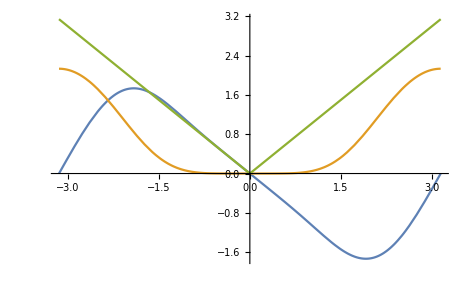

1/240 ⅈ ⅇ^(-5 ⅈ kx) (-3+25 ⅇ^(2 ⅈ kx)-225 ⅇ^(4 ⅈ kx)+128 ⅇ^(5 ⅈ kx)+75 ⅇ^(6 ⅈ kx))

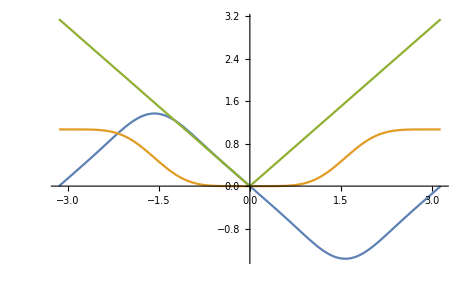

1/420 ⅈ ⅇ^(-6 ⅈ kx) (-10+63 ⅇ^(2 ⅈ kx)-210 ⅇ^(4 ⅈ kx)-35 ⅇ^(6 ⅈ kx)+192 ⅇ^(7 ⅈ kx))

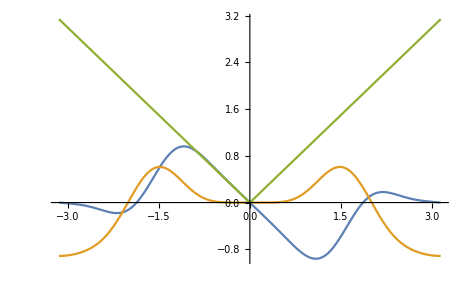

1/24 ⅈ ⅇ^(-6 ⅈ kx) (-1+6 ⅇ^(2 ⅈ kx)-18 ⅇ^(4 ⅈ kx)+10 ⅇ^(6 ⅈ kx)+3 ⅇ^(8 ⅈ kx))

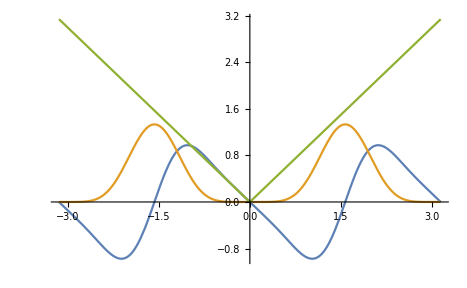

1/24 ⅈ ⅇ^(-6 ⅈ kx) (-1+6 ⅇ^(2 ⅈ kx)-18 ⅇ^(4 ⅈ kx)+10 ⅇ^(6 ⅈ kx)+3 ⅇ^(8 ⅈ kx))

-Graphics-

1/60 ⅈ ⅇ^(-4 ⅈ kx) (-1+20 ⅇ^(2 ⅈ kx)-80 ⅇ^(3 ⅈ kx)+45 ⅇ^(4 ⅈ kx)+16 ⅇ^(5 ⅈ kx))

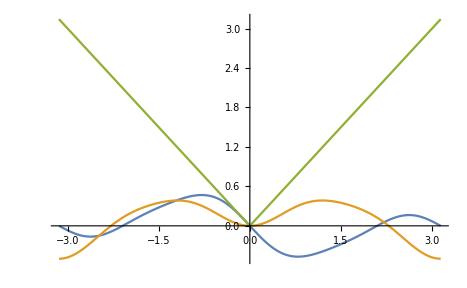

```mathematica
(*Δ=1/4;*)

idx=3;
w1[kx_, Δ_]=ω[kx]/.wSol[kx][[idx]]
w1o[kx_, Δ_]=ω[kx]/.wSolo[kx][[idx]]
Δ=1
ω[kx]/.wSolb1[kx]⟦idx⟧ //Print;
Plot[{Re[ω[kx]/.wSolb1[kx]⟦idx⟧],Im[ω[kx]/.wSolb1[kx]⟦idx⟧],Norm[kx]},{kx,-π,π}]
ω[kx]/.wSolb2[kx]⟦idx⟧ //Print;
Plot[{Re[ω[kx]/.wSolb2[kx]⟦idx⟧],Im[ω[kx]/.wSolb2[kx]⟦idx⟧],Norm[kx]},{kx,-π,π}]
ω[kx]/.wSolb3[kx]⟦idx⟧ //Print;
Plot[{Re[ω[kx]/.wSolb3[kx]⟦idx⟧],Im[ω[kx]/.wSolb3[kx]⟦idx⟧],Norm[kx]},{kx,-π,π}]
ω[kx]/.wSolb4[kx]⟦idx⟧ //Print;
Plot[{Re[ω[kx]/.wSolb4[kx]⟦idx⟧],Im[ω[kx]/.wSolb4[kx]⟦idx⟧],Norm[kx]},{kx,-π,π}]
ω[kx]/.wSolb5[kx]⟦idx⟧ //Print;
Plot[{Re[ω[kx]/.wSolb5[kx]⟦idx⟧],Im[ω[kx]/.wSolb5[kx]⟦idx⟧],Norm[kx]},{kx,-π,π}]
ω[kx]/.wSolb1[kx]⟦idx⟧ //Print;
Plot[{Re[ω[kx]/.wSoli2[kx]⟦idx⟧],Im[ω[kx]/.wSoli2[kx]⟦idx⟧],Norm[kx]},{kx,-π,π}]

(*
Plot[{Re[w1[kx,1/4]],Im[w1[kx,1/4]],Norm[kx],Re[w1o[kx,1/4]],Im[w1o[kx,1/4]]},{kx,-4π,4π}]
Plot[{Re[w1[kx,1/2]],Im[w1[kx,1/2]],Norm[kx],Re[w1o[kx,1/2]],Im[w1o[kx,1/2]]},{kx,-4π,4π}]
Plot[Im[w1o[kx,1/4]],{kx,1/40,1/2}]
Plot[Re[w1o[kx,1/4]] - Norm[kx],{kx,1/40,1/2}]*)

(*Plot[{Re[ω[kx]/.wSol2[kx]⟦idx⟧],Im[ω[kx]/.wSol2[kx]⟦idx⟧],Norm[kx]},{kx,-4π,4π}]
Plot[{Re[ω[kx]/.wSolo[kx]⟦idx⟧],Im[ω[kx]/.wSolo[kx]⟦idx⟧],Norm[kx]},{kx,-4π,4π}]
Plot[{Re[ω[kx]/.wSolo2[kx]⟦idx⟧],Im[ω[kx]/.wSolo2[kx]⟦idx⟧],Norm[kx]},{kx,-4π,4π}]*)


(*
Plot[{Re[ω[kx]/.wSoli1[kx]⟦idx⟧],Im[ω[kx]/.wSoli1[kx]⟦idx⟧],Norm[kx]},{kx,-6,6}]
Plot[{Re[ω[kx]/.wSoli2[kx]⟦idx⟧],Im[ω[kx]/.wSoli2[kx]⟦idx⟧],Norm[kx]},{kx,-6,6}]
Plot[{Re[ω[kx]/.wSoli3[kx]⟦idx⟧],Im[ω[kx]/.wSoli3[kx]⟦idx⟧],Norm[kx]},{kx,-6,6}]
*)
(*Plot[{Re[ω[kx]/.wSol[kx]⟦idx⟧],Re[ω[kx]/.wSol2[kx]⟦idx⟧],Re[ω[kx]/.wSolb1[kx]⟦idx⟧],Re[ω[kx]/.wSolb2[kx]⟦idx⟧],Re[ω[kx]/.wSolb3[kx]⟦idx⟧],Re[ω[kx]/.wSolb4[kx]⟦idx⟧],Re[ω[kx]/.wSolb5[kx]⟦idx⟧],Norm[kx]},{kx,-2π,2π}]
Plot[{Im[ω[kx]/.wSol[kx]⟦idx⟧],Im[ω[kx]/.wSol2[kx]⟦idx⟧],Im[ω[kx]/.wSolb1[kx]⟦idx⟧],Im[ω[kx]/.wSolb2[kx]⟦idx⟧],Im[ω[kx]/.wSolb3[kx]⟦idx⟧],Im[ω[kx]/.wSolb4[kx]⟦idx⟧],Im[ω[kx]/.wSolb5[kx]⟦idx⟧]},{kx,-2π,2π}]*)
(*Plot[Abs[Re[ω[kx]/.wSol[kx][[4]] ]- Re[ω[kx]/.wSolb[kx][[4]]]], {kx, -3, 3}]*)
```

```mathematica
b1 :=Function[{kx}, ω[kx]/.wSolb2[kx]⟦3⟧]
```

```mathematica
data = Table[b1[j],{j,-π,π, 0.1}];
```

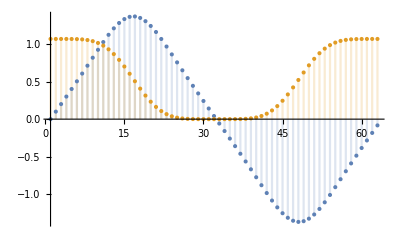

```mathematica
DiscretePlot[{Re[data[[x]]],Im[data[[x]]]},{x,1,Length[data]}]
```

```mathematica
a1 := Function[{kx},ω[kx]/.wSol[kx]⟦idx⟧]
a2 := Function[{kx},ω[kx]/.wSolb1[kx]⟦idx⟧]
a3 := Function[{kx},ω[kx]/.wSolb2[kx]⟦idx⟧]
a4 := Function[{kx},ω[kx]/.wSolb3[kx]⟦idx⟧]
a5 := Function[{kx},ω[kx]/.wSolb4[kx]⟦idx⟧]
a6 := Function[{kx},ω[kx]/.wSolb5[kx]⟦idx⟧]
a7 := Function[{kx},ω[kx]/.wSol2[kx]⟦idx⟧]
functions = {a1,a2,a3,a4,a5,a6,a7};

data = Table[Re[functions[[i]][j]],{j,-2π,2π, 0.1},{i,1,7,1}];
ListPlot3D[data]
```

-Graphics3D-

```mathematica
data2 = Table[Im[functions[[i]][j]],{j,-2π,2π, 0.1},{i,1,7,1}];
ListPlot3D[data2]
```

-Graphics3D-